Visited:  4  {{0.451116,0.788703},{0.301189,0.796556},{0.312214,0.784554},{0.458468,0.532795}}

Not visited:  5  {{0.0466549,0.103729},{0.151321,0.720935},{0.307269,0.945551},{0.618925,0.300741},{0.81643,0.811853}}

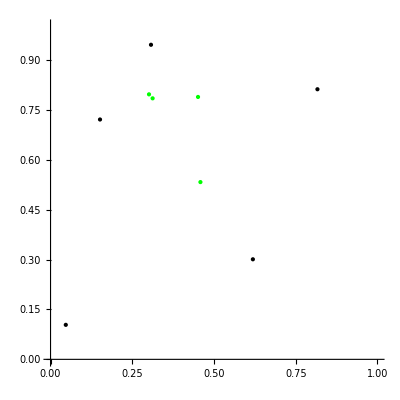

```mathematica
(* Simu Neighbours *)

n=9;

le=n;
Do[
t=Table[{Random[],Random[]},{i,n}];
td=Table[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.],{i,n}];
tdmin=Table[Min[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.]],{i,n}];
tposition=Union[Flatten[Table[Position[td[[i]],tdmin[[i]]],{i,n}]]];
If[Length[tposition]<le,tneu=t,aaa=bbb];
le=Min[{le,Length[tposition]}],{h,5000}]

td=Table[ReplacePart[Table[EuclideanDistance[tneu[[i]],tneu[[j]]],{j,n}],i->2.],{i,n}];
tdmin=Table[Min[ReplacePart[Table[EuclideanDistance[tneu[[i]],tneu[[j]]],{j,n}],i->2.]],{i,n}];
tposition=Union[Flatten[Table[Position[td[[i]],tdmin[[i]]],{i,n}]]];

t2=Table[tneu[[tposition[[m]]]],{m,Length[tposition]}];
Print["Visited:  ",le,"  ",t2]
t1=Complement[tneu,t2];
Print["Not visited:  ",n-le,"  ",t1]
Show[ListPlot[t1,PlotStyle->{Black,PointSize[Large]}],ListPlot[t2,PlotStyle->{Green,PointSize[Large]}],PlotRange->{{0,1},{0,1}},AspectRatio->1,AxesOrigin->{0,0}]
```

Test for pairwise different distances (should be 0):  0

Visited  {{0.3,0.5},{0.6,0.5}}

Not visited  {{0.045,0.67},{0.0455,0.33},{0.35,0.2},{0.355,0.8},{0.7,0.195},{0.7,0.8},{0.955,0.5}}

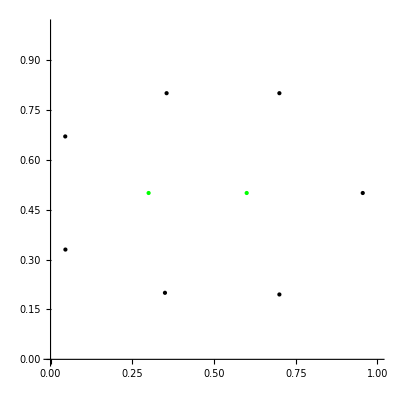

```mathematica
(* Neighbours (9,2) *)

t={{.3,.5},{.6,.5},{.955,.5},{.355,.8},{.35,.2},{.045,.67},{.0455,.33},{.7,.8},{.7,.195}};

n=Length[t];

td=Table[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.],{i,n}];
Print["Test for pairwise different distances (should be 0):  ",Length[Union[Drop[Sort[Flatten[td]],-n]]]-Binomial[n,2]]
tdmin=Table[Min[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.]],{i,n}];
tposition=Union[Flatten[Table[Position[td[[i]],tdmin[[i]]],{i,n}]]];

t2=Table[t[[tposition[[m]]]],{m,Length[tposition]}];
t1=Complement[t,t2];
Print["Visited  ",t2]
Print["Not visited  ",t1]
Show[ListPlot[t1,PlotStyle->{Black,PointSize[Large]}],ListPlot[t2,PlotStyle->{Green,PointSize[Large]}],PlotRange->{{0,1},{0,1}},AspectRatio->1,AxesOrigin->{0,0}]
```

Test for pairwise different distances (should be 0):  0

Visited  {{0.230769,0.384615},{0.461538,0.384615},{0.688462,0.384615}}

Not visited  {{0.0346154,0.515385},{0.035,0.253846},{0.265385,0.153846},{0.269231,0.615385},{0.538462,0.17},{0.538462,0.6},{0.807692,0.153077},{0.807692,0.615385},{0.961538,0.384615}}

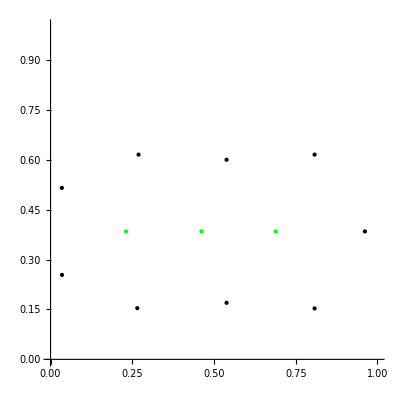

```mathematica
(* Neighbours (12,3) *)

t={{.3,.5},{.6,.5},{.895,.5},{1.25,.5},{.35,.8},{.345,.2},{.045,.67},{.0455,.33},{1.05,.8},{1.05,.199},{.7,.78},{.7,.221}}/1.3;

n=Length[t];

td=Table[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.],{i,n}];
Print["Test for pairwise different distances (should be 0):  ",Length[Union[Drop[Sort[Flatten[td]],-n]]]-Binomial[n,2]]
tdmin=Table[Min[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.]],{i,n}];
tposition=Union[Flatten[Table[Position[td[[i]],tdmin[[i]]],{i,n}]]];

t2=Table[t[[tposition[[m]]]],{m,Length[tposition]}];
t1=Complement[t,t2];
Print["Visited  ",t2]
Print["Not visited  ",t1]
Show[ListPlot[t1,PlotStyle->{Black,PointSize[Large]}],ListPlot[t2,PlotStyle->{Green,PointSize[Large]}],PlotRange->{{0,1},{0,1}},AspectRatio->1,AxesOrigin->{0,0}]
```

Test for pairwise different distances (should be 0):  0

Visited  12  {{0.0429076,0.304972},{0.503513,0.536901},{0.437182,0.465738},{0.7299,0.931306},{0.141308,0.909238},{0.362938,0.962599},{0.995759,0.582091},{0.975956,0.546681},{0.0593653,0.485206},{0.677594,0.281822},{0.497433,0.387906},{0.634686,0.97685}}

Not visited  4  {{0.298363,0.264859},{0.561932,0.0972997},{0.936393,0.096885},{0.998866,0.690008}}

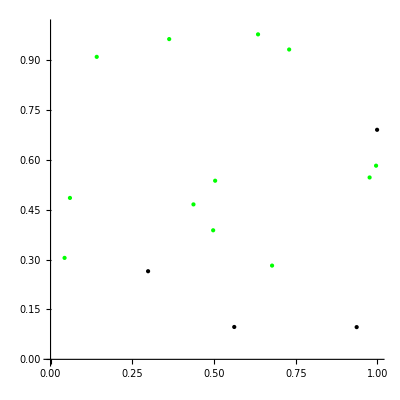

```mathematica
(* Neighbours random *)

t=Table[{Random[],Random[]},{i,16}];

n=Length[t];

td=Table[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.],{i,n}];
Print["Test for pairwise different distances (should be 0):  ",Length[Union[Drop[Sort[Flatten[td]],-n]]]-Binomial[n,2]]
tdmin=Table[Min[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.]],{i,n}];
tposition=Union[Flatten[Table[Position[td[[i]],tdmin[[i]]],{i,n}]]];

t2=Table[t[[tposition[[m]]]],{m,Length[tposition]}];
t1=Complement[t,t2];
Print["Visited  ",Length[t2],"  ",t2]
Print["Not visited  ",Length[t1],"  ",t1]
Show[ListPlot[t1,PlotStyle->{Black,PointSize[Large]}],ListPlot[t2,PlotStyle->{Green,PointSize[Large]}],PlotRange->{{0,1},{0,1}},AspectRatio->1,AxesOrigin->{0,0}]
```